```mathematica
Clear["Global`*"]
```

```mathematica
(*Setting values for the problem datas*)
nElements=1;
nOfNodesPerElement=4; 
nOfNodes =(nOfNodesPerElement-1)*nElements + 1 ;

(*Global nodes displachment vector*)
ue=Array[Symbol["ue"<>ToString[#]]&,nOfNodesPerElement];
u=Array[Symbol["u"<>ToString[#]]&,nOfNodes];

ue =ArrayReshape[ue ,{nOfNodesPerElement, 1}];
u =ArrayReshape[u ,{nOfNodes, 1}];

(*Local nodes coordinates*)
points=Array[{-1+#*2/(nOfNodesPerElement-1),0}&,nOfNodesPerElement,0];
```

```mathematica
x1=0;
x2=x1+le;

X[Xi_]:=(Xi*(x2-x1)+(x1+x2))/2;
Xi[x_]:=(2*x-(x1+x2))/(x2-x1);

(*Local shape functions & compatibility functions*)
(*Notice B0ξ == B0x = D[N0ξ/.ξ->Xi[ξ]/. ξ->x, x];*)
N0ξ = Array[InterpolatingPolynomial[ReplacePart[points,#->{points[[#,1]],1}],ξ]&, nOfNodesPerElement];
B0ξ = D[N0ξ, ξ]*D[Xi[x], x];

N0ξ =ArrayReshape[N0ξ ,{1, nOfNodesPerElement}];
B0ξ =ArrayReshape[B0ξ ,{1, nOfNodesPerElement}];
```

```mathematica
(*Local matrices and vectors in differential form*)
dfint[ξ_]:=Transpose[B0ξ]. B0ξ . ue * E0  * A0 * D[X[ξ], ξ];
dfbody[ξ_]:=R0 * A0 * b * Transpose[N0ξ] * D[X[ξ], ξ];
ftraction:=Transpose[N0ξ/.ξ->1]*A0 *τ - Transpose[N0ξ/.ξ->-1]*A0*τ;
dm[ξ_]:=R0 * A0 * Transpose[N0ξ] . N0ξ * D[X[ξ], ξ];
```

```mathematica
(*Local matrices and vectors in integral form*)
fint = Integrate[dfint[ξ], {ξ, -1, 1}];
fext = Integrate[dfbody[ξ], {ξ, -1, 1}] + ftraction;
fkin = fext-fint;
m = Integrate[dm[ξ], {ξ, -1, 1}];

(*Global matrices and vectors in integral form*)
L[e_, i_, j_]:=Piecewise[{{1,(nOfNodesPerElement-1)*(e-1)+i ==j}},0]
```

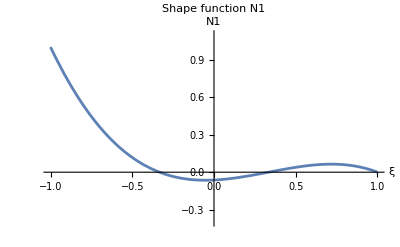

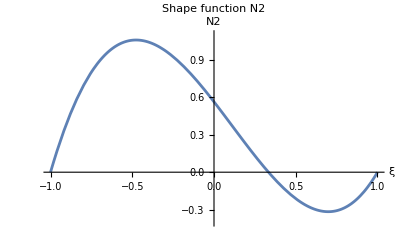

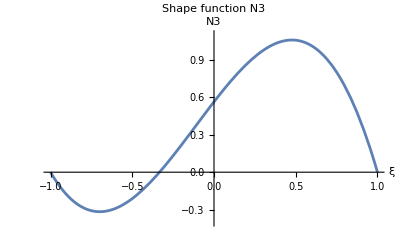

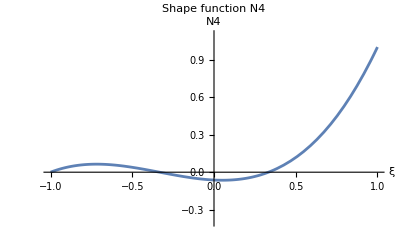

```mathematica
For[i=1,i<=nOfNodesPerElement,i++,
plot = Plot[N0ξ[[1]][[i]],{ξ,-1,1},PlotRange->{{-1,1},{-0.4,1.1}}, PlotLabel->"Shape function N"<>ToString[i],AxesLabel->{"ξ","N"<>ToString[i]}];
(*plot = Plot[B0ξ[[i]]/.le->200,{ξ,-1,1},PlotLabel->"Shape function derived B"<>ToString[i],AxesLabel->{"ξ","B"<>ToString[i]}];*)
plot //Print;
Export[FileNameJoin[{NotebookDirectory[],"latex","pdf","shape_function_N"<>ToString[i]<>".eps"}],plot];
]
```